The inertial force in the rotating frame is

F⃗=m OverVector[a_r]=-m( w⃗ x(w⃗ x r⃗) +2 w⃗ x OverVector[v_r])

Where, with respect to the center of the turntable we get

w⃗=<0,0,w>
r⃗=<x,y,0>
OverVector[v_r]=<x^·,y^·,0>

```mathematica
W={0,0,w};
r={x,y,0};
v={x',y',0};
a=Cross[-W,Cross[W , r]] -Cross[2W,v]
```

{w^2 x+2 w y',w^2 y-2 w x',0}

From which the components of the acceleration are

x^(··)=x w^2+2 y^· w

Y^(··)=y w^2+2 x^· w

Make the substitution q=x+i y

q^(··)+2i w q^·-w^2 q=0

And solve the differential equation

```mathematica
Solve[p^2+(2I w )p-w^2==0,p]
```

{{p→-ⅈ w},{p→-ⅈ w}}

q=A e^(-i w t)+B t e^(-i w t)

Which can also be written as shown in the problem description

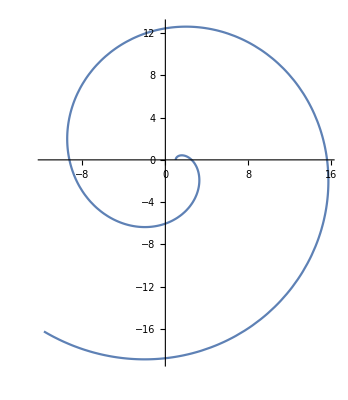

```mathematica
x0=1;
Ω=1;
vx0=0;
vy0=1;
X[t_]:=(x0+vx0 * t)*Cos[Ω*t]+(vy0+x0 *Ω)*t*Sin[Ω*t];
Y[t_]:=-(x0+vx0 * t)*Sin[Ω*t]+(vy0+x0 *Ω)*t*Cos[Ω*t];
ParametricPlot[{X[t],Y[t]},{t,0,10}]
```